# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

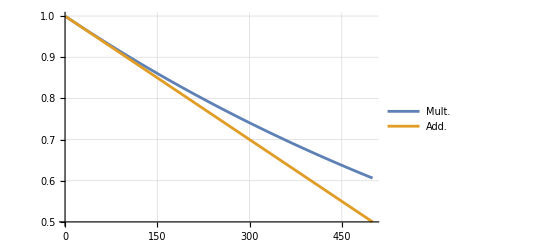

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params2={NN->1000,s->10^-2,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/100,κ→1,L→2500,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(5 (1-ⅇ^(-20 B))^3)/(2 (1+ⅇ^(-20 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
bfun02[.2]
```

0.630358

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-100]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

May need to adjust starting value (2nd argument) if this fails:

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.1]
```

0.152463

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.575646

```mathematica
getGammaHat[1,pbarExp02]
```

0.304926

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/100,κ→1,L→2500,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-1.88083 (1-0.989005^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{999.773,154.73,152.472,152.463,152.463}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Exponential example

A function to generate an expression for the effective population size depending on time (t in generations) under the expansion scenario (corresponds to equation 5):

```mathematica
NeGenExp[anf_,end_,tchange_]:=Piecewise[{{anf(end/anf)^((tchange-t)/tchange),t<tchange},{anf,t≥tchange}}]
```

The resulting expression/the demographic scenario.

```mathematica
NGE=NeGenExp[2 1000,2 30000,850]
```

Piecewise[{{2^(4+(850-t)/850) 3^((850-t)/850) 5^(3+(850-t)/850), t<850}, {2000, t≥850}, {0, True}}]

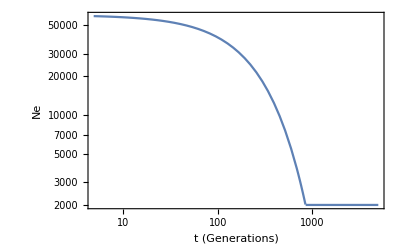

```mathematica
LogLogPlot[NGE,{t,0,5000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t (Generations)","Ne"}]
```

Equation 4 (distribution of time to coalescence, given the demographic scenario NGE - exponential increase):

```mathematica
qjtGenExp[j_,B_]:=Binomial[j,2]/(B NGE)Exp[-PiecewiseIntegrate[Binomial[j,2]/(B NGE/.t->σ),{σ,0,t}]]
```

Coalescence time for a pair of lineages under expansion model without BGS:

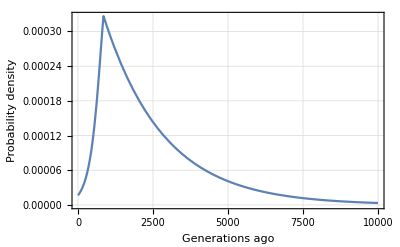

```mathematica
Plot[qjtGenExp[2,1],{t,0,10000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejGenExp[j_,B_]:=PiecewiseIntegrate[t qjtGenExp[j,B],{t,0,∞}]
```

Expected coalescence time for a pair of lineages under expansion model without BGS.

```mathematica
ejGenExp[2,1]//N
```

2596.63

Equation 8 (an expression for the probability to see b derived alleles in a sample of n with the effective population size scaled by B):

```mathematica
qnbGenExpL[n_,b_,B_]:=Sum[ejGenExp[j,B]wnbj[n,b,j],{j,2,n}]/Sum[ejGenExp[j,B]vnj[n,j],{j,2,n}]
```

As a test, derive an expression where B is set to 1 (no BGS). This does not have to be executed, and will be replicated in the last section (Including the effects of BGS - different values of B).

### Doing it on HRI

#### Smooth

An expression on Ne depending on τ

```mathematica
Nprime01
```

Piecewise[{{10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)), τ>0}, {0, True}}]

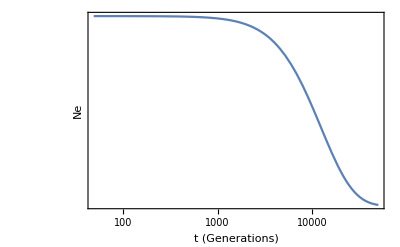

```mathematica
LogLogPlot[Nprime01,{τ,0,50000},AxesOrigin->{0,0},Frame->True,FrameLabel->{"t (Generations)","Ne"}]
```

Equation 4 (distribution of time to coalescence):

```mathematica
qjtHri01[j_]:=Binomial[j,2]/Nprime01 Exp[-Integrate[Binomial[j,2]/(Nprime01/.τ->σ),{σ,0,τ},Assumptions->{σ∈Reals,τ∈Reals}]]
```

Coalescence time for a pair of lineages under expansion model without BGS:

```mathematica
qjtHri01[2]/.τ-> 10000//AbsoluteTiming
```

{44.016,1/10000 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^10001)^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-Integrate[(ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000,{σ,0,10000},Assumptions→{σ∈ℝ,True}])}

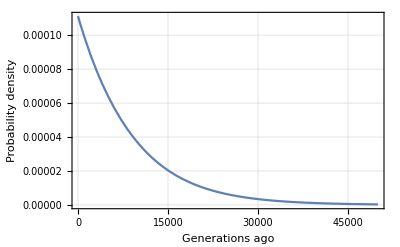

```mathematica
Plot[qjtHri01[2],{τ,0,50000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHri[j_]:=Integrate[τ qjtHri01[j],{τ,0,∞},Assumptions->{σ∈Reals,τ∈Reals}]
```

Expected coalescence time for a pair of lineages.

```mathematica
a01=(ejHri[2]//AbsoluteTiming)
```

{229.728,Integrate[1/10000 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-Integrate[(ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000,{σ,0,τ},Assumptions→{σ∈ℝ,τ∈ℝ}]) τ,{τ,0,∞},Assumptions→{σ∈ℝ,τ∈ℝ}]}

```mathematica
a01[[2]]
```

```mathematica
a02=(a01⟦2⟧//N//AbsoluteTiming)
```

NIntegrate::inumr: The integrand (ⅇ^(192/1811+«1»-Integrate[ⅇ^Plus[«2»]/10000,{σ,0,τ},Assumptions→{Element[«2»],Element[«2»]}]) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHri[n_,b_]:=Sum[ejHri[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHri[j]vnj[n,j],{j,2,n}]
```

```mathematica
Date[]
```

{2024,1,5,21,15,24.259001}

```mathematica
AbsoluteTiming[qnbHriL12b01=qnbHri[12,1]]
```

```mathematica
AbsoluteTiming[qnbHriL12b01s=qnbHriL12b01//Simplify]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

{3011.44,(3 (4522 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+16150 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+27132 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+29070 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/1000 ⅆσ) τ)/1000 ⅆτ+21945 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+12103 ∫_0^∞ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+4900 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+1428 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+285 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+35 ∫_0^∞ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+2 ∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ))/(149226 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+149226 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+48279 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+5775 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+209 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ)}

```mathematica
Hold[qnbHriL12b01]
```

Hold[qnbHriL12b01]

```mathematica
ByteCount[qnbHriL12b01]
```

$Aborted

```mathematica
SetAttributes[step,HoldAll]

step[expr_]:=Module[{P},P=(P=Return[#,TraceScan]&)&;
TraceScan[P,expr,TraceDepth->1]]
```

```mathematica
step[qnbHriL12b01s]
```

(3 (4522 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+16150 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+27132 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+29070 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/1000 ⅆσ) τ)/1000 ⅆτ+21945 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+12103 ∫_0^∞ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (21 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+4900 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+1428 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+285 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+35 ∫_0^∞ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (11 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+2 ∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ))/(149226 ∫_0^∞ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/10000 ⅆσ) τ)/10000 ⅆτ+149226 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ+48279 ∫_0^∞ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (3 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+5775 ∫_0^∞ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (7 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2500 ⅆσ) τ)/2500 ⅆτ+209 ∫_0^∞ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (9 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/2000 ⅆσ) τ)/2000 ⅆτ+∫_0^∞ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)-∫_0^τ (33 ⅇ^(192/1811+((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+σ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3)))/5000 ⅆσ) τ)/5000 ⅆτ)

```mathematica
ByteCount[qnbHriL12b01s]
```

```mathematica
AbsoluteTiming[N[qnbHriL12b01]]
```

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+«1»)^2 («1»)^3)/(10 (1+«1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
AbsoluteTiming[N[qnbHriL12b01s]]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+«1»)^2 («1»)^3)/(10 (1+«1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

{2024,1,5,22,21,42.499336}

```mathematica
AbsoluteTiming[qnbHriL12b11=qnbHri[12,11]//N]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

{2024,1,1,12,7,16.43248}

```mathematica
AbsoluteTiming[qnbHriL12=qnbHri[12,b];]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

{3841.83,Null}

```mathematica
Date[]
```

```mathematica
AbsoluteTiming[qnbHriL12b11//N]
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^(192/1811+((-1+(«1»)^(«1»))^2 (1-«1»)^3)/(10 («1»)^3)-∫_0^τ ⅇ^Plus[«2»]/10000 ⅆσ) τ)/10000 has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
qnbHriL12/.b->2//N
```

$Aborted

```mathematica
(*AbsoluteTiming[qnbHriL12=Simplify[qnbHri[12,b], TimeConstraint->1];]*)
```

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

General::stop: Further output of PolynomialGCD::lrgexp will be suppressed during this calculation.

$Aborted

```mathematica
Date[]
```

```mathematica
Table[qnbHriL12,{b,1,11}]//N
```

```mathematica
Date[]
```

$Aborted

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.88083 (1-0.989005^(1+τ))^2),999.773,152.463}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

{{x→0.,y→999.773},{x→500.,y→154.73},{x→1000.,y→152.472},{x→1500.,y→152.463},{x→2000.,y→152.463},{x→2500.,y→152.463},{x→3000.,y→152.463},{x→3500.,y→152.463},{x→4000.,y→152.463},{x→4500.,y→152.463},{x→5000.,y→152.463}}

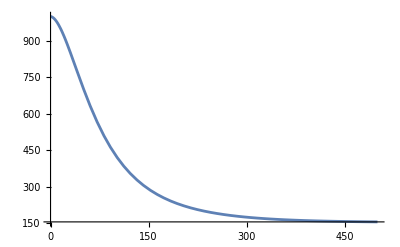

```mathematica
Plot[rAndL⟦1⟧,{τ,0,500}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.88083 (1-0.989005^(1+τ))^2),999.773,152.463}

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→56.4281},{τ→-35.8481}}

```mathematica
inv
```

{{τ→-90.4492 Log[5.17293×10^-17 (1.95463×10^16-1. √(3.82058×10^32-2.03132×10^32 Log[0.00655896228459393 y]))]},{τ→-90.4492 Log[5.1729337287279×10^-17 (1.9546302414262×10^16+√(3.8205793806978×10^32-2.0313236715796×10^32 Log[0.00655896228459393 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-90.4492 Log[5.17293×10^-17 (1.95463×10^16-1. √(3.82058×10^32-2.03132×10^32 Log[0.00655896228459393 y]))]

```mathematica
inv2/.y->660//N
```

56.4281

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,24.2873,48.5746,72.8619,97.1492,121.436,145.724,170.011,194.298,218.586,242.873}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.773,805.731,631.248,492.563,393.084,323.934,275.984,242.425,218.63,201.532,152.463}

```mathematica
xy1={xs,ys}//N
```

{{0.,24.2873,48.5746,72.8619,97.1492,121.436,145.724,170.011,194.298,218.586,242.873},{999.773,805.731,631.248,492.563,393.084,323.934,275.984,242.425,218.63,201.532,152.463}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,13.9262,27.3527,38.7983,50.2675,62.6831,76.9825,94.5943,118.347,155.721,242.873},{999.773,915.042,830.311,745.58,660.849,576.118,491.387,406.656,321.925,237.194,152.463}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-41.5887 0.989005^(1+τ) (1-0.989005^(1+τ)) ⅇ^(-1.88083 (1-0.989005^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

4.70838

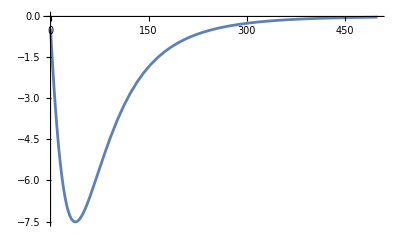

```mathematica
Plot[Nprime01p/.τ->t,{t,0,500}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Piecewise[{{999.773, x<24.2873}, {805.731, x<48.5746}, {631.248, x<72.8619}, {492.563, x<97.1492}, {393.084, x<121.436}, {323.934, x<145.724}, {275.984, x<170.011}, {242.425, x<194.298}, {218.63, x<218.586}, {201.532, x<242.873}, {152.463, x>242.873}, {0., True}}]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{999.773, x<13.9262}, {915.042, x<27.3527}, {830.311, x<38.7983}, {745.58, x<50.2675}, {660.849, x<62.6831}, {576.118, x<76.9825}, {491.387, x<94.5943}, {406.656, x<118.347}, {321.925, x<155.721}, {237.194, x<242.873}, {152.463, x>242.873}, {0., True}}]

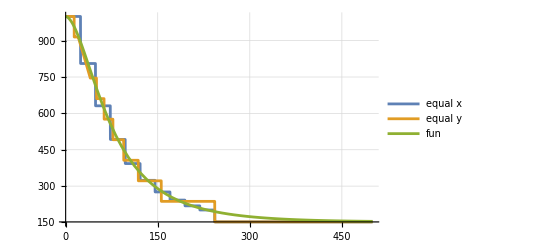

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,500},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

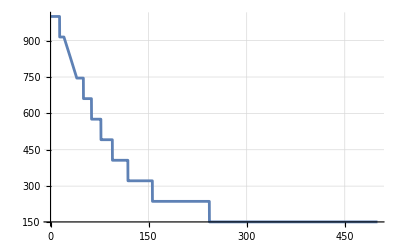

```mathematica
Plot[pwNe2/.x->t,{t,0,500},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{999.773, x<13.9262}, {915.042, x<27.3527}, {830.311, x<38.7983}, {745.58, x<50.2675}, {660.849, x<62.6831}, {576.118, x<76.9825}, {491.387, x<94.5943}, {406.656, x<118.347}, {321.925, x<155.721}, {237.194, x<242.873}, {152.463, x>242.873}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

152.463

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

```mathematica
qjtHriPw01smooth[j_]:=Binomial[j,2]/np02 Exp[-Integrate[Binomial[j,2]/(np02/.τ->σ),{σ,0,τ},Assumptions->τ∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{0.951646,0.000319594}

```mathematica
qjtHriPw01smooth[2]/.τ-> 600//N//AbsoluteTiming
```

{3.46896,0.000846223}

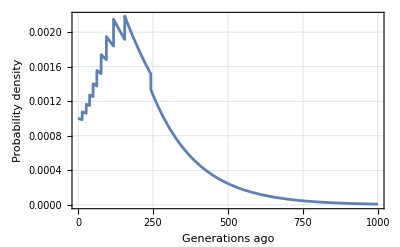

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

```mathematica
(*ejHriPwSmooth[j_]:=Integrate[τ qjtHriPw01smooth[j],{τ,0,∞}, Assumptions->τ∈Reals]*)
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{12.5439,269.091}

```mathematica
(*a01smooth=(ejHriPwSmooth[2]//AbsoluteTiming)*)
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

NIntegrate::nlim: σ = τ is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

NIntegrate::nlim: σ = τ is not a valid limit of integration.

NIntegrate::precw: The precision of the argument function ((ⅇ^(1.02344 (1-(«19»)^(Plus«1»«1»]))^2))/1000) is less than WorkingPrecision (30.9546).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::nlim: σ = τ is not a valid limit of integration.

General::stop: Further output of NIntegrate::nlim will be suppressed during this calculation.

{31.2302,Integrate[(ⅇ^(1.02344 (1-0.997098^(1+τ))^2-Integrate[(ⅇ^(1.02344 (1-0.997098^(1+σ))^2))/1000,{σ,0,τ},Assumptions→τ∈ℝ&&τ>0]) τ)/1000,{τ,0,∞},Assumptions→τ∈ℝ]}

```mathematica
a01[[2]]
```

599.115

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
AbsoluteTiming[n12b1=qnbHriPw[12,1]]
```

{220.314,0.413224}

Equal x steps

{253.907,0.340639}

2 steps 30s, 3 steps 70s, 4 steps 263s, 5 steps 1334s (22min)
With Assumptions x ∈R:
5steps 206s, 6 steps 270, 7 steps 355, 8 steps 394s, 9 steps 435s

Duration similar irrespective of b.

```mathematica
(*n12All=AbsoluteTiming[n12b1=qnbHriPw[12,#]]&/@Range[1,11]*)
```

{{212.535,0.413224},{177.512,0.177479},{176.77,0.105818},{175.299,0.0728697},{174.444,0.0545042},{173.993,0.0430248},{173.701,0.035276},{173.393,0.0297467},{173.1,0.0256311},{175.457,0.0224646},{174.973,0.0199623}}

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{157.514,0.52746},{128.762,0.173417},{127.74,0.0913076},{127.303,0.0593491},{126.505,0.0432564},{124.797,0.0338087},{124.516,0.0276793},{124.322,0.0234183},{123.958,0.0203041}}

```mathematica
Export["v03sfs10.txt", n10All]
```

v03sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{298.998,0.464436},{264.8,0.163722},{265.043,0.086754},{264.212,0.0554903},{263.847,0.0395542},{263.679,0.0302215},{263.492,0.0242182},{263.296,0.0200871},{263.079,0.0170972},{263.106,0.014847},{262.789,0.0131004},{262.618,0.0117103},{262.585,0.0105809},{262.535,0.00964748},{262.419,0.00886465},{262.313,0.00819994},{262.295,0.00762944},{262.078,0.0071352},{261.9,0.00670346}}

```mathematica
Export["v03sfs20.txt", n20All]
```

v03sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{633.195,0.411191},{566.919,0.157527},{566.528,0.0863743},{565.524,0.0557768},{565.305,0.0396459},{565.508,0.0300245},{565.725,0.0237832},{566.289,0.0194792},{565.849,0.0163694},{566.205,0.0140384},{565.21,0.0122386},{564.782,0.0108145},{564.859,0.00966454},{565.079,0.00871962},{565.226,0.0079316},{565.243,0.00726592},{565.346,0.00669722},{565.381,0.00620656},{564.956,0.0057795},{564.968,0.00540488},{564.919,0.00507396},{565.309,0.00477979},{565.232,0.0045168},{565.394,0.00428047},{565.494,0.00406709},{565.642,0.00387359},{565.33,0.00369743},{565.285,0.00353648},{565.352,0.00338891},{564.825,0.00325321},{565.137,0.00312804},{565.404,0.00301229},{565.25,0.00290497},{565.509,0.00280525},{565.333,0.00271236},{565.477,0.00262568},{565.538,0.00254462},{565.513,0.00246868},{565.817,0.00239742}}

```mathematica
Export["v03sfs40.txt", n40All]
```

v03sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1330.34,0.361648},{1208.63,0.149967},{1204.39,0.0861376},{1202.74,0.0571591},{1213.2,0.0412508},{1203.04,0.0314721},{1203.45,0.0249867},{1202.52,0.0204421},{1202.15,0.0171213},{1202.65,0.014613},{1202.9,0.0126668},{1202.08,0.0111227},{1202.7,0.00987432},{1202.46,0.00884872},{1202.98,0.00799433},{1202.8,0.00727385},{1202.49,0.00665977},{1202.69,0.00613137},{1202.72,0.00567282},{1202.16,0.00527184},{1202.14,0.00491879},{1202.63,0.00460598},{1202.79,0.00432724},{1202.25,0.00407757},{1203.01,0.00385286},{1201.82,0.00364973},{1202.06,0.00346535},{1201.79,0.00329737},{1202.07,0.00314378},{1202.12,0.0030029},{1202.67,0.00287328},{1202.,0.00275368},{1201.99,0.00264304},{1201.99,0.00254043},{1202.34,0.00244504},{1201.31,0.00235616},{1201.49,0.00227319},{1205.92,0.00219557},{1198.35,0.00212283},{1198.07,0.00205453},{1198.24,0.00199031},{1198.32,0.00192982},{1197.75,0.00187275},{1197.58,0.00181885},{1197.46,0.00176786},{1197.31,0.00171956},{1197.57,0.00167375},{1197.71,0.00163026},{1198.49,0.00158892},{1202.97,0.00154958},{1197.59,0.0015121},{1197.22,0.00147637},{1198.45,0.00144227},{1199.4,0.00140969},{1199.01,0.00137854},{1198.66,0.00134873},{1199.09,0.00132018},{1198.9,0.00129282},{1198.56,0.00126657},{1198.8,0.00124137},{1199.26,0.00121717},{1199.08,0.00119391},{1200.04,0.00117154},{1199.15,0.00115001},{1198.84,0.00112927},{1198.53,0.00110929},{1199.37,0.00109002},{1197.38,0.00107144},{1198.14,0.0010535},{1198.45,0.00103618},{1197.38,0.00101944},{1197.45,0.00100326},{1197.56,0.000987616},{1197.44,0.000972478},{1202.49,0.000957823},{1198.89,0.000943632},{1197.39,0.000929883},{1197.58,0.000916556},{1197.33,0.000903634}}

```mathematica
Export["v03sfs80.txt", n80All]
```

v03sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11